# Holographic 𝒜

Hier das Worksheet für die “finalen” Ergebnisse der Einsteinkorrigierenden Funktion 𝒜.
Dieses Worksheet generiert insbesondere auch die Plots, die in der Masterarbeit verwendet werden.

Es basiert auf “Holo-Calc13.nb” was wiederum auf Calc12 basiert.
Es sind einflüsse aus Calc17 reingeflossen, wo der Code fuer GUP ueberarbeitet wurde.

## 0. Definitionen

```mathematica
holo[z_,n_] = z^(2+n) / (z^(2+n) + 1);
hD[z_,n_] = D[holo[z,n],z] // Together
(* das grosse V aus der Thesis, der 3+n Integration Kernel *)
bigV[z_,n_] = 1 / z^(2+n)  hD[ z,n]
(* das kleine v aus der Thesis, 1d integraion kernel *)
vSide[z_,n_, sign_:1] = z^(1+n) If[sign<0,(-1)^n bigV[-z,n], bigV[z,n]] 
vEff[z_,n_] = vSide[z,n,+1] HeavisideTheta@Re@z + vSide[z,n,-1] HeavisideTheta@Re[-z]
```

((2+n) z^(1+n))/((1+z^(2+n))^2)

(2+n)/(z (1+z^(2+n))^2)

z^(1+n) If[sign<0,(-1)^n bigV[-z,n],bigV[z,n]]

-((-1)^n (2+n) z^n HeavisideTheta[-Re[z]])/((1+(-z)^(2+n))^2)+((2+n) z^n HeavisideTheta[Re[z]])/((1+z^(2+n))^2)

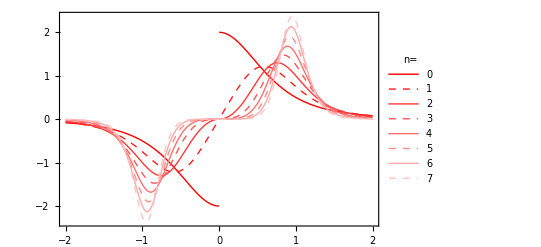

```mathematica
Plot[Table[vEff[z,n],{n,0,7}] //Evaluate, {z,-2,2},
PlotStyle-> MapIndexed[{If[EvenQ@First@#2, Dashed,{}],Blend[{Red,White},#1]}&, Rescale@Range@10],
(*PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),*)
PlotLegends-> LineLegend[Table[n,{n,0,7}],LegendLabel-> "n="],
Frame-> True
]
```

## 1. Polstellen extrahieren

```mathematica
ReduceToSolutions[reduceResult_, extractVariable_] := Cases[reduceResult,Equal[extractVariable, value_]-> value, 100]
polReduce[n_, side_] := Reduce[Denominator@vSide[q,n, side]==0,q]
polstellenSide[n_,side_] := polReduce[n,side]~ ReduceToSolutions ~ q
polstellen[n_] := Join@@(Select[polstellenSide[n,#[[1]]], #[[2]]]&) /@ {
+1 ->  (Re[#] ≥ 0&),
-1 -> (Re[#] < 0&)
}
mitgenommenePolstellen[n_] := Select[polstellen[n], Im[#]≤  0&]
```

```mathematica
(* Zeichne die Polstellen.
Diese Funktion/Zelle ist aus Polstellen.nb kopiert und etwas modifiziert. *)
Daten[n_] :={
{Re[#], Im[#]} & /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a}) , (* in Blau *)
{Re[#], Im[#]} & /@ polstellenSide[n, +1],
{Re[#], Im[#]} & /@ polstellenSide[n, -1],
{Re[#], Im[#]} & /@ polstellen[n] (* schwarz *),
{Re[#], Im[#]} & /@ mitgenommenePolstellen[n]
}
MakePlot[n_,
label_:"Left and right hand poles"
] :=Show[ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},
PlotMarkers -> {
{Graphics[{Lighter@Blue, Opacity[0.3],Disk[]}], 0.05},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12},
{Graphics[{Red,Thickness[0.15],Circle[]}],0.18}
},
PlotRange-> All,
ImageSize->Medium],
Graphics[{Opacity[0.2],Circle[{0,0},1]}]
];
Manipulate[Show[
MakePlot[n],
Graphics[{Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{120,130},{0,0}]](*,
Text[Style[StringForm["# Residuen=``",ResidueList[n]//Length],{Black, 20}], Offset[{+30,-30},{0,0}]]*)}
]]
,{n,0,8,1}]
```

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# unique poles", "# poles","Unique Poles"}},
Table[{n,
Length@Union@polstellen[n],
Length@polstellen[n],
Union@polstellen[n] // Sort
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # unique poles | # poles | Unique Poles
0 | 2 | 2 | {-ⅈ,ⅈ}
1 | 4 | 4 | {-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}
2 | 4 | 4 | {-(-1)^(1/4),(-1)^(1/4),-(-1)^(3/4),(-1)^(3/4)}
3 | 4 | 4 | {-(-1)^(1/5),(-1)^(1/5),-(-1)^(4/5),(-1)^(4/5)}
4 | 6 | 6 | {-ⅈ,ⅈ,-(-1)^(1/6),(-1)^(1/6),-(-1)^(5/6),(-1)^(5/6)}
5 | 8 | 8 | {-(-1)^(1/7),(-1)^(1/7),-(-1)^(3/7),(-1)^(3/7),-(-1)^(4/7),(-1)^(4/7),-(-1)^(6/7),(-1)^(6/7)}
6 | 8 | 8 | {-(-1)^(1/8),(-1)^(1/8),-(-1)^(3/8),(-1)^(3/8),-(-1)^(5/8),(-1)^(5/8),-(-1)^(7/8),(-1)^(7/8)}
7 | 8 | 8 | {-(-1)^(1/9),(-1)^(1/9),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(8/9),(-1)^(8/9)}

## Integralberechnung

```mathematica
IntegralResidueList[n_] := 
(2 Pi I) * (-1)  * Residue[vSide[z, n, Sign@Re@#] * Exp[-I q z], {z,#}]& /@ mitgenommenePolstellen[n]
IntegralValue[n_] := Total@IntegralResidueList[n]
AValue[n_] := 1/(2π)^(2+n) (*2 Pi I*) / q * IntegralValue[n]
```

#### Manuelles Nachvollziehen der Residuen

Hier wird nochmal einen Schritt zurückgegangen und nur die rechte Seite angeschaut, mit ihren Polen.

```mathematica
resFunk = vSide[z,n,+1] / (2+n)
With[{show = Grid[{#,Arg@#} ,Frame-> All] &},
Grid[{{"n","alle Polstellen von f_+", "Residues f_+", "Test"}}~Join~Table[{n,
show@polstellenSide[n,+1],
show[Residue[resFunk,{z,#}]&/@ polstellenSide[n, +1]]
},{n,0,7}], Frame-> All, Alignment-> {Left, Left}]]
```

z^n/((1+z^(2+n))^2)

n | alle Polstellen von f_+ | Residues f_+ | Test
0 | -ⅈ | ⅈ
-π/2 | π/2 | ⅈ/4 | -ⅈ/4
π/2 | -π/2 | 
1 | -1 | (-1)^(1/3) | -(-1)^(2/3)
π | π/3 | -π/3 | -1/9 | -1/9 (-1)^(2/3) | 1/9 (-1)^(1/3)
π | -π/3 | π/3 | 
2 | -(-1)^(1/4) | (-1)^(1/4) | -(-1)^(3/4) | (-1)^(3/4)
-(3 π)/4 | π/4 | -π/4 | (3 π)/4 | 1/16 (-1)^(3/4) | -1/16 (-1)^(3/4) | 1/16 (-1)^(1/4) | -1/16 (-1)^(1/4)
(3 π)/4 | -π/4 | π/4 | -(3 π)/4 | 
3 | -1 | (-1)^(1/5) | -(-1)^(2/5) | (-1)^(3/5) | -(-1)^(4/5)
π | π/5 | -(3 π)/5 | (3 π)/5 | -π/5 | -1/25 | -1/25 (-1)^(4/5) | 1/25 (-1)^(3/5) | -1/25 (-1)^(2/5) | 1/25 (-1)^(1/5)
π | -π/5 | (3 π)/5 | -(3 π)/5 | π/5 | 
4 | -ⅈ | ⅈ | -(-1)^(1/6) | (-1)^(1/6) | -(-1)^(5/6) | (-1)^(5/6)
-π/2 | π/2 | -(5 π)/6 | π/6 | -π/6 | (5 π)/6 | ⅈ/36 | -ⅈ/36 | 1/36 (-1)^(5/6) | -1/36 (-1)^(5/6) | 1/36 (-1)^(1/6) | -1/36 (-1)^(1/6)
π/2 | -π/2 | (5 π)/6 | -π/6 | π/6 | -(5 π)/6 | 
5 | -1 | (-1)^(1/7) | -(-1)^(2/7) | (-1)^(3/7) | -(-1)^(4/7) | (-1)^(5/7) | -(-1)^(6/7)
π | π/7 | -(5 π)/7 | (3 π)/7 | -(3 π)/7 | (5 π)/7 | -π/7 | -1/49 | -1/49 (-1)^(6/7) | 1/49 (-1)^(5/7) | -1/49 (-1)^(4/7) | 1/49 (-1)^(3/7) | -1/49 (-1)^(2/7) | 1/49 (-1)^(1/7)
π | -π/7 | (5 π)/7 | -(3 π)/7 | (3 π)/7 | -(5 π)/7 | π/7 | 
6 | -(-1)^(1/8) | (-1)^(1/8) | -(-1)^(3/8) | (-1)^(3/8) | -(-1)^(5/8) | (-1)^(5/8) | -(-1)^(7/8) | (-1)^(7/8)
-(7 π)/8 | π/8 | -(5 π)/8 | (3 π)/8 | -(3 π)/8 | (5 π)/8 | -π/8 | (7 π)/8 | 1/64 (-1)^(7/8) | -1/64 (-1)^(7/8) | 1/64 (-1)^(5/8) | -1/64 (-1)^(5/8) | 1/64 (-1)^(3/8) | -1/64 (-1)^(3/8) | 1/64 (-1)^(1/8) | -1/64 (-1)^(1/8)
(7 π)/8 | -π/8 | (5 π)/8 | -(3 π)/8 | (3 π)/8 | -(5 π)/8 | π/8 | -(7 π)/8 | 
7 | -1 | (-1)^(1/9) | -(-1)^(2/9) | (-1)^(1/3) | -(-1)^(4/9) | (-1)^(5/9) | -(-1)^(2/3) | (-1)^(7/9) | -(-1)^(8/9)
π | π/9 | -(7 π)/9 | π/3 | -(5 π)/9 | (5 π)/9 | -π/3 | (7 π)/9 | -π/9 | -1/81 | -1/81 (-1)^(8/9) | 1/81 (-1)^(7/9) | -1/81 (-1)^(2/3) | 1/81 (-1)^(5/9) | -1/81 (-1)^(4/9) | 1/81 (-1)^(1/3) | -1/81 (-1)^(2/9) | 1/81 (-1)^(1/9)
π | -π/9 | (7 π)/9 | -π/3 | (5 π)/9 | -(5 π)/9 | π/3 | -(7 π)/9 | π/9 |

```mathematica
-1/3 (-1)^(1/3) ⅇ^((-1)^(1/6) q) (-1+(-1)^(1/6) q)//FullSimplify
```

1/3 ⅇ^((-1)^(1/6) q) ((-1)^(1/3)-ⅈ q)

```mathematica
vSide[z, 1, Sign@Re[-(-1)^(2/3)]]
```

(3 z)/((1+z^3)^2)

```mathematica
D[(3 z)/((1+z^3)^2)  Exp[PONY * z],z]
```

-(18 ⅇ^(PONY z) z^3)/((1+z^3)^3)+(3 ⅇ^(PONY z))/((1+z^3)^2)+(3 ⅇ^(PONY z) PONY z)/((1+z^3)^2)

```mathematica
Residue[(3 z)/((1+z^3)^(22/33))  Exp[PONY * z],{z,-(-1)^(2/3)}]
```

Residue[(3 ⅇ^(PONY z) z)/((1+z^3)^(2/3)),{z,-(-1)^(2/3)}]

```mathematica
Residue[(3 z)/((1+z^3)^2)  ,{z,-(-1)^(2/3)}]
```

1/3 (-1)^(1/3)

```mathematica
With[{show = Grid[{#,Arg@#} ,Frame-> All] &},
Grid[{{"n","polis","selbstberechnet"}}~Join~Table[With[{
A = (Function[{z0},If[Sign@Re@z0 ≥ 0,+1,-1] Conjugate[z0]/(n+2)Exp[I z0 q]( 1- I z0 q)]/@mitgenommenePolstellen[n] ),
B=( Residue[vSide[z, n, Sign@Re@#] Exp[I q z],{z,#}]&/@ mitgenommenePolstellen[n] )
},{n,
(*show@mitgenommenePolstellen[n],*)
A,B,FullSimplify[A - B]
}],{n,0,7}], Frame-> All, Alignment-> {Left, Left}]]
```

n | polis | selbstberechnet | 
0 | {1/2 ⅈ ⅇ^q (1-q)} | {-1/2 ⅈ ⅇ^q (-1+q)} | {0}
1 | {1/3 (1/2+(ⅈ √3)/2) ⅇ^((-1)^(1/6) q) (1-(-1)^(1/6) q),-1/3 (-1/2+(ⅈ √3)/2) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)} | {-1/3 (-1)^(1/3) ⅇ^((-1)^(1/6) q) (-1+(-1)^(1/6) q),-1/3 (-1)^(2/3) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)} | {0,0}
2 | {((1/4+ⅈ/4) ⅇ^((-1)^(1/4) q) (1-(-1)^(1/4) q))/(√2),((1/4-ⅈ/4) ⅇ^(-(-1)^(3/4) q) (1+(-1)^(3/4) q))/(√2)} | {1/4 ⅇ^((-1)^(1/4) q) ((-1)^(1/4)-ⅈ q),-1/4 ⅇ^(-(-1)^(3/4) q) ((-1)^(3/4)-ⅈ q)} | {0,0}
3 | {1/5 (ⅈ √(5/8-(√5)/8)+1/4 (1+√5)) ⅇ^((-1)^(3/10) q) (1-(-1)^(3/10) q),-1/5 (1/4 (-1-√5)+ⅈ √(5/8-(√5)/8)) ⅇ^(-(-1)^(7/10) q) (1+(-1)^(7/10) q)} | {-1/5 (-1)^(1/5) ⅇ^((-1)^(3/10) q) (-1+(-1)^(3/10) q),-1/5 ⅈ ⅇ^(-(-1)^(7/10) q) ((-1)^(3/10)-q)} | {0,0}
4 | {1/6 ⅈ ⅇ^q (1-q),1/6 (ⅈ/2+(√3)/2) ⅇ^((-1)^(1/3) q) (1-(-1)^(1/3) q),-1/6 (ⅈ/2-(√3)/2) ⅇ^(-(-1)^(2/3) q) (1+(-1)^(2/3) q)} | {-1/6 ⅈ ⅇ^q (-1+q),-1/6 (-1)^(1/6) ⅇ^((-1)^(1/3) q) (-1+(-1)^(1/3) q),1/6 (-1)^(1/3) ⅇ^(-(-1)^(2/3) q) (-ⅈ+(-1)^(1/6) q)} | {0,0,0}
5 | {1/7 ⅇ^((-1)^(1/14) q) (1-(-1)^(1/14) q) (ⅈ Cos[π/14]+Sin[π/14]),1/7 ⅇ^((-1)^(5/14) q) (1-(-1)^(5/14) q) (Cos[π/7]+ⅈ Sin[π/7]),-1/7 ⅇ^(-(-1)^(9/14) q) (1+(-1)^(9/14) q) (-Cos[π/7]+ⅈ Sin[π/7]),-1/7 ⅇ^(-(-1)^(13/14) q) (1+(-1)^(13/14) q) (ⅈ Cos[π/14]-Sin[π/14])} | {-1/7 (-1)^(3/7) ⅇ^((-1)^(1/14) q) (-1+(-1)^(1/14) q),-1/7 (-1)^(1/7) ⅇ^((-1)^(5/14) q) (-1+(-1)^(5/14) q),-1/7 ⅈ ⅇ^(-(-1)^(9/14) q) ((-1)^(5/14)-q),-1/7 ⅈ ⅇ^(-(-1)^(13/14) q) ((-1)^(1/14)-q)} | {0,0,0,0}
6 | {1/8 ⅇ^((-1)^(1/8) q) (1-(-1)^(1/8) q) (ⅈ Cos[π/8]+Sin[π/8]),1/8 ⅇ^((-1)^(3/8) q) (1-(-1)^(3/8) q) (Cos[π/8]+ⅈ Sin[π/8]),-1/8 ⅇ^(-(-1)^(5/8) q) (1+(-1)^(5/8) q) (-Cos[π/8]+ⅈ Sin[π/8]),-1/8 ⅇ^(-(-1)^(7/8) q) (1+(-1)^(7/8) q) (ⅈ Cos[π/8]-Sin[π/8])} | {-1/8 (-1)^(3/8) ⅇ^((-1)^(1/8) q) (-1+(-1)^(1/8) q),-1/8 (-1)^(1/8) ⅇ^((-1)^(3/8) q) (-1+(-1)^(3/8) q),-1/8 ⅈ ⅇ^(-(-1)^(5/8) q) ((-1)^(3/8)-q),-1/8 ⅈ ⅇ^(-(-1)^(7/8) q) ((-1)^(1/8)-q)} | {0,0,0,0}
7 | {1/9 (1/2+(ⅈ √3)/2) ⅇ^((-1)^(1/6) q) (1-(-1)^(1/6) q),1/9 ⅇ^((-1)^(7/18) q) (1-(-1)^(7/18) q) (Cos[π/9]+ⅈ Sin[π/9]),-1/9 ⅇ^(-(-1)^(11/18) q) (1+(-1)^(11/18) q) (-Cos[π/9]+ⅈ Sin[π/9]),-1/9 (-1/2+(ⅈ √3)/2) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)} | {-1/9 (-1)^(1/3) ⅇ^((-1)^(1/6) q) (-1+(-1)^(1/6) q),-1/9 (-1)^(1/9) ⅇ^((-1)^(7/18) q) (-1+(-1)^(7/18) q),-1/9 ⅈ ⅇ^(-(-1)^(11/18) q) ((-1)^(7/18)-q),-1/9 (-1)^(2/3) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)} | {0,0,0,0}

```mathematica
With[{show = Grid[{#,Arg@#} ,Frame-> All] &},
Grid[{{"n","alle Polstellen von f_+", "Residues f_+", "Test"}}~Join~Table[{n,
show@mitgenommenePolstellen[n],
show[ Residue[vSide[z, n, Sign@Re@#],{z,#}]&/@ mitgenommenePolstellen[n]],
(*show[ vSide[z, n, Sign@Re@#]&/@ mitgenommenePolstellen[n]],*)
show[ Residue[vSide[z, n, Sign@Re@#] Exp[I q z],{z,#}]&/@ mitgenommenePolstellen[n]],
},{n,0,7}], Frame-> All, Alignment-> {Left, Left}]]
```

n | alle Polstellen von f_+ | Residues f_+ | Test | 
0 | -ⅈ
-π/2 | ⅈ/2
π/2 | -1/2 ⅈ ⅇ^q (-1+q)
Arg[-ⅈ ⅇ^q (-1+q)] | 
1 | -(-1)^(2/3) | -(-1)^(1/3)
-π/3 | -(2 π)/3 | 1/3 (-1)^(1/3) | -1/3 (-1)^(2/3)
π/3 | -π/3 | -1/3 (-1)^(1/3) ⅇ^((-1)^(1/6) q) (-1+(-1)^(1/6) q) | -1/3 (-1)^(2/3) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)
Arg[-(-1)^(1/3) ⅇ^((-1)^(1/6) q) (-1+(-1)^(1/6) q)] | Arg[-(-1)^(2/3) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)] | 
2 | -(-1)^(3/4) | -(-1)^(1/4)
-π/4 | -(3 π)/4 | 1/4 (-1)^(1/4) | -1/4 (-1)^(3/4)
π/4 | -π/4 | 1/4 ⅇ^((-1)^(1/4) q) ((-1)^(1/4)-ⅈ q) | -1/4 ⅇ^(-(-1)^(3/4) q) ((-1)^(3/4)-ⅈ q)
Arg[ⅇ^((-1)^(1/4) q) ((-1)^(1/4)-ⅈ q)] | Arg[-ⅇ^(-(-1)^(3/4) q) ((-1)^(3/4)-ⅈ q)] | 
3 | -(-1)^(4/5) | -(-1)^(1/5)
-π/5 | -(4 π)/5 | 1/5 (-1)^(1/5) | -1/5 (-1)^(4/5)
π/5 | -π/5 | -1/5 (-1)^(1/5) ⅇ^((-1)^(3/10) q) (-1+(-1)^(3/10) q) | -1/5 ⅈ ⅇ^(-(-1)^(7/10) q) ((-1)^(3/10)-q)
Arg[-(-1)^(1/5) ⅇ^((-1)^(3/10) q) (-1+(-1)^(3/10) q)] | Arg[-ⅈ ⅇ^(-(-1)^(7/10) q) ((-1)^(3/10)-q)] | 
4 | -ⅈ | -(-1)^(5/6) | -(-1)^(1/6)
-π/2 | -π/6 | -(5 π)/6 | ⅈ/6 | 1/6 (-1)^(1/6) | -1/6 (-1)^(5/6)
π/2 | π/6 | -π/6 | -1/6 ⅈ ⅇ^q (-1+q) | -1/6 (-1)^(1/6) ⅇ^((-1)^(1/3) q) (-1+(-1)^(1/3) q) | 1/6 (-1)^(1/3) ⅇ^(-(-1)^(2/3) q) (-ⅈ+(-1)^(1/6) q)
Arg[-ⅈ ⅇ^q (-1+q)] | Arg[-(-1)^(1/6) ⅇ^((-1)^(1/3) q) (-1+(-1)^(1/3) q)] | Arg[(-1)^(1/3) ⅇ^(-(-1)^(2/3) q) (-ⅈ+(-1)^(1/6) q)] | 
5 | -(-1)^(4/7) | -(-1)^(6/7) | -(-1)^(1/7) | -(-1)^(3/7)
-(3 π)/7 | -π/7 | -(6 π)/7 | -(4 π)/7 | 1/7 (-1)^(3/7) | 1/7 (-1)^(1/7) | -1/7 (-1)^(6/7) | -1/7 (-1)^(4/7)
(3 π)/7 | π/7 | -π/7 | -(3 π)/7 | -1/7 (-1)^(3/7) ⅇ^((-1)^(1/14) q) (-1+(-1)^(1/14) q) | -1/7 (-1)^(1/7) ⅇ^((-1)^(5/14) q) (-1+(-1)^(5/14) q) | -1/7 ⅈ ⅇ^(-(-1)^(9/14) q) ((-1)^(5/14)-q) | -1/7 ⅈ ⅇ^(-(-1)^(13/14) q) ((-1)^(1/14)-q)
Arg[-(-1)^(3/7) ⅇ^((-1)^(1/14) q) (-1+(-1)^(1/14) q)] | Arg[-(-1)^(1/7) ⅇ^((-1)^(5/14) q) (-1+(-1)^(5/14) q)] | Arg[-ⅈ ⅇ^(-(-1)^(9/14) q) ((-1)^(5/14)-q)] | Arg[-ⅈ ⅇ^(-(-1)^(13/14) q) ((-1)^(1/14)-q)] | 
6 | -(-1)^(5/8) | -(-1)^(7/8) | -(-1)^(1/8) | -(-1)^(3/8)
-(3 π)/8 | -π/8 | -(7 π)/8 | -(5 π)/8 | 1/8 (-1)^(3/8) | 1/8 (-1)^(1/8) | -1/8 (-1)^(7/8) | -1/8 (-1)^(5/8)
(3 π)/8 | π/8 | -π/8 | -(3 π)/8 | -1/8 (-1)^(3/8) ⅇ^((-1)^(1/8) q) (-1+(-1)^(1/8) q) | -1/8 (-1)^(1/8) ⅇ^((-1)^(3/8) q) (-1+(-1)^(3/8) q) | -1/8 ⅈ ⅇ^(-(-1)^(5/8) q) ((-1)^(3/8)-q) | -1/8 ⅈ ⅇ^(-(-1)^(7/8) q) ((-1)^(1/8)-q)
Arg[-(-1)^(3/8) ⅇ^((-1)^(1/8) q) (-1+(-1)^(1/8) q)] | Arg[-(-1)^(1/8) ⅇ^((-1)^(3/8) q) (-1+(-1)^(3/8) q)] | Arg[-ⅈ ⅇ^(-(-1)^(5/8) q) ((-1)^(3/8)-q)] | Arg[-ⅈ ⅇ^(-(-1)^(7/8) q) ((-1)^(1/8)-q)] | 
7 | -(-1)^(2/3) | -(-1)^(8/9) | -(-1)^(1/9) | -(-1)^(1/3)
-π/3 | -π/9 | -(8 π)/9 | -(2 π)/3 | 1/9 (-1)^(1/3) | 1/9 (-1)^(1/9) | -1/9 (-1)^(8/9) | -1/9 (-1)^(2/3)
π/3 | π/9 | -π/9 | -π/3 | -1/9 (-1)^(1/3) ⅇ^((-1)^(1/6) q) (-1+(-1)^(1/6) q) | -1/9 (-1)^(1/9) ⅇ^((-1)^(7/18) q) (-1+(-1)^(7/18) q) | -1/9 ⅈ ⅇ^(-(-1)^(11/18) q) ((-1)^(7/18)-q) | -1/9 (-1)^(2/3) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)
Arg[-(-1)^(1/3) ⅇ^((-1)^(1/6) q) (-1+(-1)^(1/6) q)] | Arg[-(-1)^(1/9) ⅇ^((-1)^(7/18) q) (-1+(-1)^(7/18) q)] | Arg[-ⅈ ⅇ^(-(-1)^(11/18) q) ((-1)^(7/18)-q)] | Arg[-(-1)^(2/3) ⅇ^(-(-1)^(5/6) q) (1+(-1)^(5/6) q)] |

```mathematica
IntegralResidueList[0]
```

{ⅇ^-q π (1+q)}

```mathematica
Conjugate[q] Exp[I q z] + Conjugate[-q] Exp[I (-q) z] //FullSimplify
```

2 ⅈ Conjugate[q] Sin[q z]

```mathematica
Exp[I q z] - Exp[-I q z] // FullSimplify
```

2 ⅈ Sin[q z]

```mathematica
Sign@Re[+I]
```

0

#### Endergebnis

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# poles","Wert für A(p)"}},
Table[{n,
Length@mitgenommenePolstellen[n],
AValue[n] ,
AValue[n] //ComplexExpand
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # poles | Wert für A(p) | 
0 | 1 | (ⅇ^-q (1+q))/(4 π q) | ⅇ^-q/(4 π)+ⅇ^-q/(4 π q)
1 | 2 | 1/(8 π^3 q)(-2/3 ⅇ^((-1)^(5/6) q) π ((-1)^(1/6)+q)-2/3 (-1)^(5/6) ⅇ^(-(-1)^(1/6) q) π (1+(-1)^(1/6) q)) | ⅈ (-(ⅇ^(-(√3 q)/2) Cos[q/2])/(12 π^2 q)-(ⅇ^(-(√3 q)/2) Sin[q/2])/(6 π^2)-(ⅇ^(-(√3 q)/2) Sin[q/2])/(4 √3 π^2 q))
2 | 2 | 1/(16 π^4 q)(-1/2 ⅈ ⅇ^(-(-1)^(1/4) q) π ((-1)^(1/4)+ⅈ q)+1/2 ⅈ ⅇ^((-1)^(3/4) q) π ((-1)^(3/4)+ⅈ q)) | ⅈ (-(ⅇ^(-q/(√2)) Cos[q/(√2)])/(16 √2 π^3 q)-(ⅇ^(-q/(√2)) Sin[q/(√2)])/(16 π^3)-(ⅇ^(-q/(√2)) Sin[q/(√2)])/(16 √2 π^3 q))
3 | 2 | 1/(32 π^5 q)(-2/5 ⅇ^((-1)^(7/10) q) π ((-1)^(3/10)+q)-2/5 (-1)^(7/10) ⅇ^(-(-1)^(3/10) q) π (1+(-1)^(3/10) q)) | (ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (-1-√5) q])/(80 π^4)+(√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (-1-√5) q])/(80 π^4 q)-(ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (1+√5) q])/(80 π^4)-(√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (1+√5) q])/(80 π^4 q)+(ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (-1-√5) q])/(320 π^4 q)+(ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (-1-√5) q])/(64 √5 π^4 q)+(ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (1+√5) q])/(320 π^4 q)+(ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (1+√5) q])/(64 √5 π^4 q)+ⅈ (-(ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (-1-√5) q])/(320 π^4 q)-(ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (-1-√5) q])/(64 √5 π^4 q)-(ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (1+√5) q])/(320 π^4 q)-(ⅇ^(-√(5/8-(√5)/8) q) Cos[1/4 (1+√5) q])/(64 √5 π^4 q)+(ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (-1-√5) q])/(80 π^4)+(√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (-1-√5) q])/(80 π^4 q)-(ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (1+√5) q])/(80 π^4)-(√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) q) Sin[1/4 (1+√5) q])/(80 π^4 q))
4 | 3 | 1/(64 π^6 q)(1/3 ⅇ^-q π (1+q)+1/3 (-1)^(5/6) ⅇ^((-1)^(2/3) q) π (ⅈ+(-1)^(1/6) q)-1/3 (-1)^(2/3) ⅇ^(-(-1)^(1/3) q) π (1+(-1)^(1/3) q)) | ⅇ^-q/(192 π^5)+ⅇ^-q/(192 π^5 q)+ⅈ (-(ⅇ^(-q/2) Cos[(√3 q)/2])/(64 √3 π^5 q)-(ⅇ^(-q/2) Sin[(√3 q)/2])/(96 π^5)-(ⅇ^(-q/2) Sin[(√3 q)/2])/(192 π^5 q))
5 | 4 | 1/(128 π^7 q)(-2/7 ⅇ^((-1)^(13/14) q) π ((-1)^(1/14)+q)-2/7 ⅇ^((-1)^(9/14) q) π ((-1)^(5/14)+q)-2/7 (-1)^(13/14) ⅇ^(-(-1)^(1/14) q) π (1+(-1)^(1/14) q)-2/7 (-1)^(9/14) ⅇ^(-(-1)^(5/14) q) π (1+(-1)^(5/14) q)) | -(ⅇ^(-q Sin[π/7]) Cos[q Cos[π/7]])/(448 π^6)+(ⅇ^(-q Sin[π/7]) Cos[π/7]^2 Cos[q Cos[π/7]])/(448 π^6)-(ⅇ^(-q Cos[π/14]) Cos[q Sin[π/14]])/(448 π^6)+(ⅇ^(-q Cos[π/14]) Cos[π/14]^2 Cos[q Sin[π/14]])/(448 π^6)+(ⅇ^(-q Cos[π/14]) Cos[q Sin[π/14]] Sin[π/14]^2)/(448 π^6)+(ⅇ^(-q Sin[π/7]) Cos[q Cos[π/7]] Sin[π/7]^2)/(448 π^6)+ⅈ (-(ⅇ^(-q Sin[π/7]) Cos[π/7] Cos[q Cos[π/7]])/(224 π^6 q)-(ⅇ^(-q Cos[π/14]) Cos[q Sin[π/14]] Sin[π/14])/(224 π^6 q)-(ⅇ^(-q Sin[π/7]) Sin[q Cos[π/7]])/(448 π^6)-(ⅇ^(-q Sin[π/7]) Cos[π/7]^2 Sin[q Cos[π/7]])/(448 π^6)-(ⅇ^(-q Sin[π/7]) Sin[π/7] Sin[q Cos[π/7]])/(224 π^6 q)-(ⅇ^(-q Sin[π/7]) Sin[π/7]^2 Sin[q Cos[π/7]])/(448 π^6)-(ⅇ^(-q Cos[π/14]) Sin[q Sin[π/14]])/(448 π^6)-(ⅇ^(-q Cos[π/14]) Cos[π/14] Sin[q Sin[π/14]])/(224 π^6 q)-(ⅇ^(-q Cos[π/14]) Cos[π/14]^2 Sin[q Sin[π/14]])/(448 π^6)-(ⅇ^(-q Cos[π/14]) Sin[π/14]^2 Sin[q Sin[π/14]])/(448 π^6))
6 | 4 | 1/(256 π^8 q)(-1/4 ⅇ^((-1)^(7/8) q) π ((-1)^(1/8)+q)-1/4 ⅇ^((-1)^(5/8) q) π ((-1)^(3/8)+q)-1/4 (-1)^(7/8) ⅇ^(-(-1)^(1/8) q) π (1+(-1)^(1/8) q)-1/4 (-1)^(5/8) ⅇ^(-(-1)^(3/8) q) π (1+(-1)^(3/8) q)) | -(ⅇ^(-q Sin[π/8]) Cos[q Cos[π/8]])/(1024 π^7)+(ⅇ^(-q Sin[π/8]) Cos[π/8]^2 Cos[q Cos[π/8]])/(1024 π^7)-(ⅇ^(-q Cos[π/8]) Cos[q Sin[π/8]])/(1024 π^7)+(ⅇ^(-q Cos[π/8]) Cos[π/8]^2 Cos[q Sin[π/8]])/(1024 π^7)+(ⅇ^(-q Sin[π/8]) Cos[q Cos[π/8]] Sin[π/8]^2)/(1024 π^7)+(ⅇ^(-q Cos[π/8]) Cos[q Sin[π/8]] Sin[π/8]^2)/(1024 π^7)+ⅈ (-(ⅇ^(-q Sin[π/8]) Cos[π/8] Cos[q Cos[π/8]])/(512 π^7 q)-(ⅇ^(-q Cos[π/8]) Cos[q Sin[π/8]] Sin[π/8])/(512 π^7 q)-(ⅇ^(-q Sin[π/8]) Sin[q Cos[π/8]])/(1024 π^7)-(ⅇ^(-q Sin[π/8]) Cos[π/8]^2 Sin[q Cos[π/8]])/(1024 π^7)-(ⅇ^(-q Sin[π/8]) Sin[π/8] Sin[q Cos[π/8]])/(512 π^7 q)-(ⅇ^(-q Sin[π/8]) Sin[π/8]^2 Sin[q Cos[π/8]])/(1024 π^7)-(ⅇ^(-q Cos[π/8]) Sin[q Sin[π/8]])/(1024 π^7)-(ⅇ^(-q Cos[π/8]) Cos[π/8] Sin[q Sin[π/8]])/(512 π^7 q)-(ⅇ^(-q Cos[π/8]) Cos[π/8]^2 Sin[q Sin[π/8]])/(1024 π^7)-(ⅇ^(-q Cos[π/8]) Sin[π/8]^2 Sin[q Sin[π/8]])/(1024 π^7))
7 | 4 | 1/(512 π^9 q)(-2/9 ⅇ^((-1)^(5/6) q) π ((-1)^(1/6)+q)-2/9 ⅇ^((-1)^(11/18) q) π ((-1)^(7/18)+q)-2/9 (-1)^(5/6) ⅇ^(-(-1)^(1/6) q) π (1+(-1)^(1/6) q)-2/9 (-1)^(11/18) ⅇ^(-(-1)^(7/18) q) π (1+(-1)^(7/18) q)) | -(ⅇ^(-q Sin[π/9]) Cos[q Cos[π/9]])/(2304 π^8)+(ⅇ^(-q Sin[π/9]) Cos[π/9]^2 Cos[q Cos[π/9]])/(2304 π^8)+(ⅇ^(-q Sin[π/9]) Cos[q Cos[π/9]] Sin[π/9]^2)/(2304 π^8)+ⅈ (-(ⅇ^(-(√3 q)/2) Cos[q/2])/(2304 π^8 q)-(ⅇ^(-q Sin[π/9]) Cos[π/9] Cos[q Cos[π/9]])/(1152 π^8 q)-(ⅇ^(-(√3 q)/2) Sin[q/2])/(1152 π^8)-(ⅇ^(-(√3 q)/2) Sin[q/2])/(768 √3 π^8 q)-(ⅇ^(-q Sin[π/9]) Sin[q Cos[π/9]])/(2304 π^8)-(ⅇ^(-q Sin[π/9]) Cos[π/9]^2 Sin[q Cos[π/9]])/(2304 π^8)-(ⅇ^(-q Sin[π/9]) Sin[π/9] Sin[q Cos[π/9]])/(1152 π^8 q)-(ⅇ^(-q Sin[π/9]) Sin[π/9]^2 Sin[q Cos[π/9]])/(2304 π^8))